# model fit for netlogo modeling yixia@home Aug 21, 2010 -Graphics-

FittedModel[0.70471/(1+x)^2.28299]

{ | Estimate | Standard Error | t Statistic | P-Value
β | 1.59521 | 0.0504247 | 31.6355 | 5.92644×10^-7
γ | 1.28299 | 0.124305 | 10.3213 | 0.000146863,0.997566}

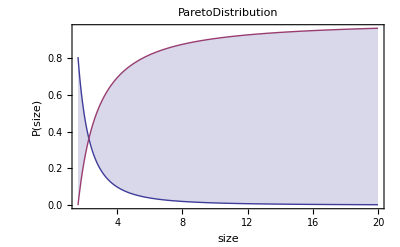

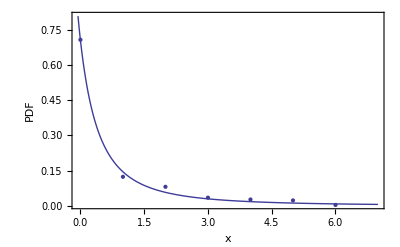

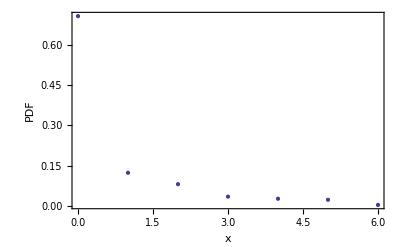

```mathematica
data={{0,183/259},{1,32/259},{2,21/259},{3,9/259}, {4,7/259},{5,6/259},{6,1/259}};
nlm=NonlinearModelFit[data,β^(-γ)(x+1)^(-1-γ)γ,{β,γ},x]
nlm[{"ParameterTable","RSquared"}]
Plot[{PDF[ParetoDistribution[1.5952091488714142,1.2829889844211193],x],CDF[ParetoDistribution[1.5952091488714142,1.2829889844211193],x]},{x,1.5952091488714142,20},Filling->{1->{2}},Frame->True,FrameLabel->{size,P[size]},PlotLabel->ParetoDistribution,LabelStyle->Purple]
Show[ListPlot[data],Plot[nlm[x],{x,-1,7}],Frame->True,FrameLabel->{x,PDF},LabelStyle->Purple]
Show[ListPlot[data],Frame->True,FrameLabel->{x,PDF},LabelStyle->Purple]
```